{{0.,0.},{21.5,16.36},{40.6,30.89},{55.6,42.33},{69.8,53.01},{85.5,64.89},{99.8,75.69}}

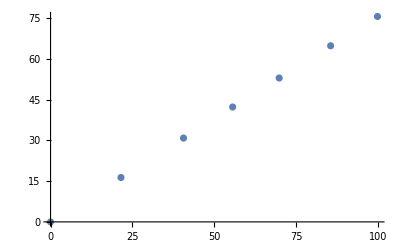

```mathematica
T={0.0,21.5,40.6,55.6,69.8,85.5,99.8};
U={0.00,16.36,30.89,42.33,53.01,64.89,75.69};
data=Table[{T[[i]],U[[i]]},{i,1,7}]
pd=ListPlot[data]
```

```mathematica
fd=Fit[data,{1,x},x]
```

0.0611633+0.758428 x

```mathematica
Needs["LinearRegression`"]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Regress[data,{1,x},x,RegressionReport->{RSquared}]
```

```mathematica
{RSquared->0.9999954836744178}
```

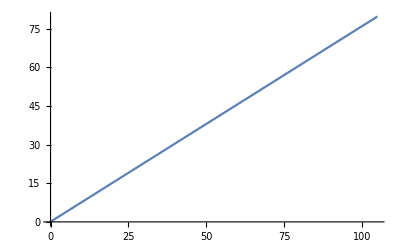

```mathematica
Plot[fd,{x,0,105}]
```

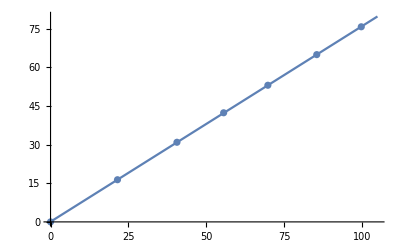

```mathematica
Show[%,pd]
```

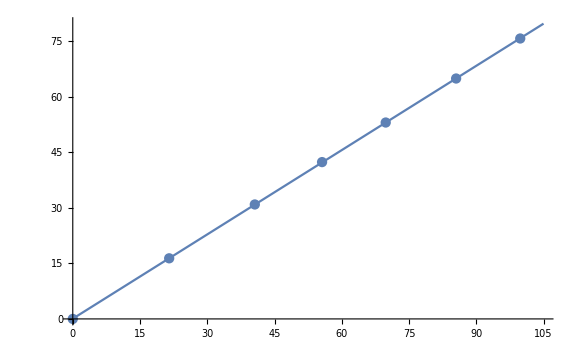

```mathematica
Show[%33,ImageSize->Large]
```

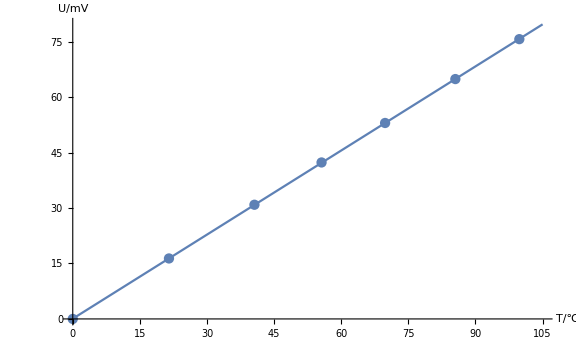

```mathematica
Show[%34,AxesLabel->{HoldForm[T/℃],HoldForm[U/mV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```